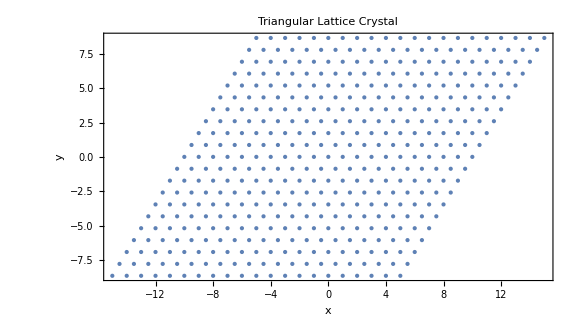

```mathematica
(* Define the lattice vector *)
A1={1,0}; 

A2={1/2,Sqrt[3]/2};
(* Number of lattice points in each direction *)
n=10; 
(* Lattice generation and visualization *)
TriX=Flatten[Table[A1*i+A2*j,{i,-n,n},{j,-n,n}],1];
plotLattice = ListPlot[TriX,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Triangular Lattice Crystal", ImageSize->Large]
```

```mathematica
(* Size of skyrmion *)
size = 2;
(* Translation vectors *)
T1 = {size+size/2,(√3)/2 size, 0}
T2 = {0, √3 size, 0}
T3 = {0,0,1};
volume = T1.(T2×T3);
(* Reciprocal lattice vectors *)
B1 = (2 π)/volume(T2×T3)
B2 = (2 π)/volume(T3×T1)
```

{3,√3,0}

{0,2 √3,0}

{(2 π)/3,0,0}

{-π/3,π/(√3),0}

```mathematica
(* Spin texture implimentation - Triple Q state of SkX*)
(* direction vectors of each spin helix in superposition *)
basisVectors ={{-1,0}, {1/2,-Sqrt[3]/2}, {1/2, Sqrt[3]/2}};(* skyrmion directions *)
(*basisVectors ={{0,-1}, {-Sqrt[3]/2,1/2}, {Sqrt[3]/2,1/2}}; (* Anti skyrmion directions *)*)
(* The reciprocal space lattice vectors *)
QVectors ={{B1[[1]],B1[[2]]}, {B2[[1]], B2[[2]]}, {B2[[1]], -B2[[2]]}};
(* Initail phase or epoch *)
epoch={Pi/3,Pi/3,Pi/3};
(* Spin texture *)
mxy [x_, y_] := Total[Table[(Sin[QVectors[[i]].{x,y}+epoch[[i]] ]) basisVectors[[i]],{i,1,3}]]
mz[x_, y_] :=  Total[Table[(Cos[QVectors[[i]].{x,y} +epoch[[i]]]),{i,1,3}]]
(* Spin texture function to get the 3D tuples *)
spins[x_, y_] := {N[mxy[x, y].{1,0}],N[ mxy[x, y].{0,1}], N[mz[x,y]]}
(* Visualization of the spin texture *)
(* Position vectors as 3D tuples *)
POSlist = Table[{TriX[[i]][[1]],TriX[[i]][[2]],0},{i,1,Length[TriX]}];
(* Generating the spin texture and normalizing them *)
texture =Table[spins[TriX[[i]][[1]], TriX[[i]][[2]]],{i, 1, Length[TriX]}]// N// Chop;
NORMtext = Table[texture[[i]]/Norm[texture[[i]]],{i,1,Length[texture]}];
(* Plotting the spin texture *)
cylinders = Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],Cylinder[{POSlist[[i]]-NORMtext[[i]]/2,POSlist[[i]]},1/10]}},{i,1,Length[TriX] }];

cones= Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],
Cone[{POSlist[[i]],POSlist[[i]]+NORMtext[[i]]/2},1/5]}},{i,1,Length[TriX] }];

texturePlot=Graphics3D[{cylinders,cones},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Full, Lighting->{{"Ambient",White}} ]
```

-Graphics3D-

```mathematica
Show[texturePlot,ViewPoint->Above]
```

-Graphics3D-

```mathematica
(* Isolating single skyrmion position tuples *)
UNITcells={};
(* Bounds of unit cell *)
Xlow = -size;
Xhigh = size/2;
Ylow [x_]:=T1⟦2⟧/T1⟦1⟧(x + size)
Yhigh [x_]:=T1⟦2⟧/T1⟦1⟧(x + size) + Norm[T2]
(* Unitcell from Sublattice 1 *)
For[i = 1, i<= Length[TriX],i++,
If[
TriX[[i]][[1]]>=Xlow && TriX[[i]][[1]]<Xhigh , 
If[TriX[[i]][[2]]>=Ylow[TriX[[i]][[1]]] && TriX[[i]][[2]]<Yhigh[TriX[[i]][[1]]],
AppendTo[UNITcells, {TriX[[i]][[1]], TriX[[i]][[2]]}]]]]
UNITcells;
UNITcells//Dimensions;
```

```mathematica
UNITcells;
```

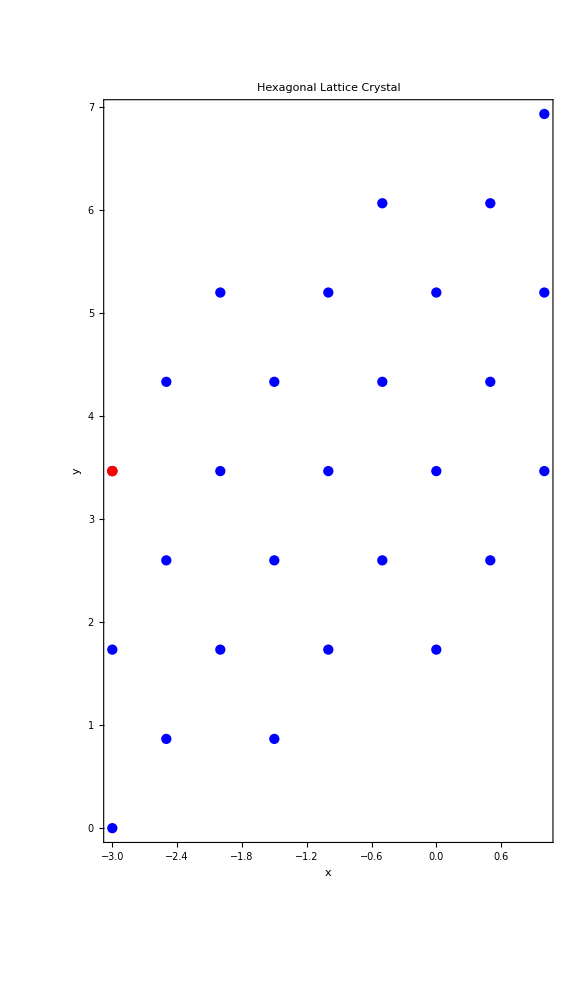

```mathematica
plot1 = ListPlot[UNITcells,PlotStyle->{Blue},AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Hexagonal Lattice Crystal", ImageSize->Large];
plot3 = ListPlot[{UNITcells[[1]]},PlotStyle->Red];
Show[plot1,plot3,PlotRange->All]
```

```mathematica
(* Visualization of the spin texture *)
(* Position vectors as 3D tuples *)
POSlist = Table[{UNITcells[[i]][[1]],UNITcells[[i]][[2]],0},{i,1,Length[UNITcells]}];
(* Generating the spin texture and normalizing them *)
texture =Table[spins[UNITcells[[i]][[1]], UNITcells[[i]][[2]]],{i, 1, Length[UNITcells]}]// N// Chop;
NORMtext = Table[texture[[i]]/Norm[texture[[i]]],{i,1,Length[texture]}];
(* Plotting the spin texture *)
cylinders = Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],Cylinder[{POSlist[[i]]-NORMtext[[i]]/2,POSlist[[i]]},1/10]}},{i,1,Length[UNITcells] }];

cones= Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],
Cone[{POSlist[[i]],POSlist[[i]]+NORMtext[[i]]/2},1/5]}},{i,1,Length[UNITcells] }];

texturePlot=Graphics3D[{cylinders,cones},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Medium,ViewPoint->Top, Lighting->{{"Ambient",White}} ]
```

-Graphics3D-

```mathematica
(* Neighbour table for Periodic Boundary condition Implimentation *)
(* Convention *)
L1N1 = {1,0};
L1N2 = {-1,0};
L1N3 = {1/2,(√3)/2};
L1N4 = {-1/2,-(√3)/2};
L1N5 ={-1/2,(√3)/2};
L1N6 = {1/2,(-√3)/2};
S1NN1 ={};
S1NN2 ={};
S1NN3 ={};
S1NN4 ={};
S1NN5={};
S1NN6 ={};

For[i=1,i<=Length[UNITcells], i++,
For[j=1,j<=Length[UNITcells],j++ ,
If[UNITcells[[j]] == UNITcells[[i]] + L1N1,AppendTo[S1NN1,j],
If [UNITcells[[j]] == UNITcells[[i]] + L1N1+{T2[[1]],T2[[2]]}, AppendTo[S1NN1,j],
If[UNITcells[[j]]==UNITcells[[i]] + L1N1 -{T1[[1]], T1[[2]]}, AppendTo[S1NN1,j]] ]]]];

For[i =1, i<= Length[UNITcells], i++,
For[j=1,j<=Length[UNITcells], j++ ,
If[UNITcells[[j]] == UNITcells[[i]]+ L1N2,AppendTo[S1NN2,j],
If[UNITcells[[j]] == UNITcells[[i]]  + L1N2 + {T1[[1]], T1[[2]]}, AppendTo[S1NN2 , j],
If[UNITcells[[j]] == UNITcells[[i]] + L1N2 - {T2[[1]], T2[[2]] }, AppendTo[S1NN2,j]] ]  ] ]];

For[i =1 , i <= Length[UNITcells], i++,
For[j =1 , j<= Length[UNITcells], j ++, 
If[UNITcells[[j]] == UNITcells[[i]] + L1N3, AppendTo[S1NN3,j],
If[UNITcells[[j]] == UNITcells[[i]] + L1N3  - {T1[[1]],T1[[2]]} - {T2[[1]], T2[[2]]}, AppendTo[S1NN3,j],
If[UNITcells[[j]] == UNITcells[[i]] + L1N3 -{T1[[1]], T1[[2]]}, AppendTo[S1NN3,j],
If[UNITcells[[j]] == UNITcells[[i]] + L1N3 -{T2[[1]], T2[[2]]}, AppendTo[S1NN3,j]]]]]     ]]

For[i =1 , i <= Length[UNITcells], i++,
For[j =1 , j<= Length[UNITcells], j ++, 
If[UNITcells[[j]] == UNITcells[[i]] + L1N4, AppendTo[S1NN4,j], 
If[UNITcells[[j]] == UNITcells[[i]] + L1N4 + {T1[[1]],T1[[2]]} + {T2[[1]], T2[[2]]} , AppendTo[S1NN4,j], 
If[UNITcells[[j]] == UNITcells[[i]] + L1N4 +{T2[[1]], T2[[2]]},AppendTo[S1NN4,j],
 If[UNITcells[[j]] == UNITcells[[i]] + L1N4 +{T1[[1]], T1[[2]]},AppendTo[S1NN4,j]] ] ]]]]

For[i =1 , i <= Length[UNITcells], i++,
For[j =1 , j<= Length[UNITcells], j ++, 
If[UNITcells[[j]] == UNITcells[[i]] + L1N5, AppendTo[S1NN5,j],  
If[UNITcells[[j]] == UNITcells[[i]] + L1N5 +{T1[[1]], T1[[2]]},AppendTo[S1NN5,j], 
If[UNITcells[[j]] == UNITcells[[i]] + L1N5 -{T2[[1]], T2[[2]]},AppendTo[S1NN5,j]] ]]]]

For[i =1 , i <= Length[UNITcells], i++,
For[j =1 , j<= Length[UNITcells], j ++, 
If[UNITcells[[j]] == UNITcells[[i]] + L1N6, AppendTo[S1NN6,j], 
If[UNITcells[[j]] == UNITcells[[i]] + L1N6 + {T2[[1]], T2[[2]]} , AppendTo[S1NN6,j],   
If[UNITcells[[j]] == UNITcells[[i]] + L1N6 - {T1[[1]], T1[[2]]} , AppendTo[S1NN6,j]]]      ]]]
```

```mathematica
sfield =Chop[N[Table[spins[UNITcells[[i]][[1]],UNITcells[[i]][[2]]],{i, 1, Length[UNITcells]}]]];
spinfield = Table[sfield[[i]]/Norm[sfield[[i]]],{i,1,Length[sfield]}];
```

```mathematica
(* Converting to Spherical Polar Coordinates *)
SpinPOLAR=CoordinateTransform["Cartesian"->"Spherical",spinfield]/.Indeterminate->0;
SpinPOLAR//MatrixForm;
SpinPOLAR = Table[If[SpinPOLAR[[i]][[3]]<0, {SpinPOLAR[[i]][[1]],SpinPOLAR[[i]][[2]],SpinPOLAR[[i]][[3]] + 2 Pi}, SpinPOLAR[[i]]],{i,1,Length[SpinPOLAR]}];
SpinPOLAR//MatrixForm;
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

```mathematica
θ =Table[SpinPOLAR[[i]][[2]],{i,1,Length[SpinPOLAR]}];
ϕ =Table[SpinPOLAR[[i]][[3]],{i,1,Length[SpinPOLAR]}];
```

```mathematica
KetArray = Table[{Cos[1/2 θ⟦i⟧], Sin[1/2 θ⟦i⟧] ⅇ^(ⅈ ϕ⟦i⟧)},{i,1,Length[SpinPOLAR]}]//Chop;
KetArray// MatrixForm;
(* The conjugate vector of the spin texture |χ⟩, ⟨χ|:=|χ⟩† *)

BraArray = Table[Conjugate[KetArray[[i]]],{i,1,Length[KetArray]}];
```

```mathematica
(*Parameters*)
 t = 1;
dres = 0.0;
```

```mathematica
(*Hamiltonian*)
N1={1,0};
N2={-1,0};
N3={1/2,(√3)/2};
N4 = {-1/2,(-√3)/2};
N5={-1/2,(√3)/2};
N6={1/2,-(√3)/2};
K[kx_, ky_] := {kx, ky}
(* Hamiltonian matrix *)
Hij[kx_, ky_] := Module[{hopingProduct},
hopingProduct = ConstantArray[0,{Length[SpinPOLAR],Length[SpinPOLAR]}];
For[i = 1, i<= Length[SpinPOLAR], i++,
hopingProduct[[i]][[S1NN1[[i]]]] = t BraArray[[i]].KetArray[[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].N1)  +  I dres  BraArray[[i]].(N1[[1]]*PauliMatrix[1]-N1[[2]]*PauliMatrix[2]).KetArray[[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].N1)  ;

hopingProduct[[i]][[S1NN2[[i]]]] = t BraArray[[i]].KetArray[[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].N2) +  I dres  BraArray[[i]].(N2[[1]]*PauliMatrix[1]-N2[[2]]*PauliMatrix[2]).KetArray[[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].N2);

hopingProduct[[i]][[S1NN3[[i]]]] = t BraArray[[i]].KetArray[[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].N3)+I dres BraArray[[i]].(N3[[1]]*PauliMatrix[1]-N3[[2]]*PauliMatrix[2]).KetArray[[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].N3);

hopingProduct[[i]][[S1NN4[[i]]]] = t BraArray[[i]].KetArray[[S1NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].N4)  + I dres BraArray[[i]].(N4[[1]]*PauliMatrix[1]-N4[[2]]*PauliMatrix[2]).KetArray[[S1NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].N4) ;

hopingProduct[[i]][[S1NN5[[i]]]] = t BraArray[[i]].KetArray[[S1NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].N5) + I dres BraArray[[i]].(N5[[1]]*PauliMatrix[1]-N5[[2]]*PauliMatrix[2]).KetArray[[S1NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].N5);

hopingProduct[[i]][[S1NN6[[i]]]] = t BraArray[[i]].KetArray[[S1NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].N6) +  I dres BraArray[[i]].(N6[[1]]*PauliMatrix[1]- N6[[2]]*PauliMatrix[2]).KetArray[[S1NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].N6);

];
hopingProduct
]
Hij[kx, ky]// MatrixForm;
ConjugateTranspose[Hij[0,1]]== Hij[0,1]
```

True

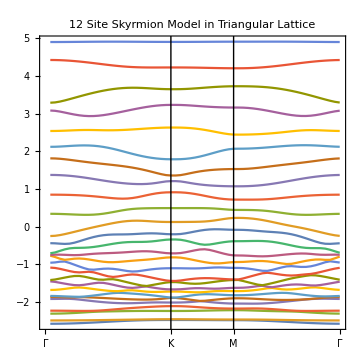

```mathematica
Ev[kx_,ky_] := Sort[Eigenvalues[Hij[kx, ky]] ]
(* Collection of Eigen values along the irreducible path in the reciprocal space *)
d=25; (* step count *)

tabGK[n_]:=Table[Ev[k,k/Sqrt[3]][[n]],{k,0,Norm[B1]/2,Norm[B1]/(2 d)}];
tabKM[n_]:=Table[Ev[Norm[B1]/2,ky][[n]],{ky,Norm[B1]/(2 Sqrt[3]),0,-(Norm[B1]/(Sqrt[3] d))}];
tabMG[n_]:=Table[Ev[kx,0][[n]],{kx,Norm[B1]/2,0,-(Norm[B1]/(2*0.87*d))}];

l1=Length[tabGK[1]];
l2=l1+Length[tabKM[1]];
l3=l2+Length[tabMG[1]];
customTicksX={{0,Style["Γ",Bold]},{l1,Style["K",Bold]},{l2,Style["M",Bold]},{l3,Style["Γ",Bold]}};

vl1=Graphics[{Line[{{l1,-20},{l1,20}}]},AspectRatio->1];

vl2=Graphics[{Line[{{l2,-20},{l2,20}}]},AspectRatio->1];

join[i_]:= Join[tabGK[i],tabKM[i],tabMG[i]]
bands := Table[join[i],{i,1,Length[UNITcells]}];
Show[ListLinePlot[bands,ImageSize->Medium,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{customTicksX,None}},Axes->False,Frame->True,PlotLabel->"12 Site Skyrmion Model in Triangular Lattice",FrameTicksStyle->Directive[Bold,Black]], vl1, vl2]
```

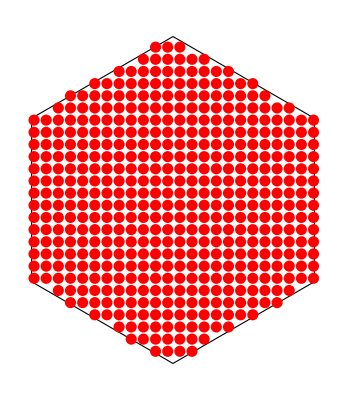

{479,2}

```mathematica
(*Side length of the hexagon*)
sideLength=Norm[B1]/(√3);
(*Define the hexagonal domain*)
hexagon=Polygon[Table[sideLength {Sin[2 π k/6],Cos[2 π k/6]},{k,6}]];
(*Distance between grid points*)
distance=0.06;
(*Generate a grid of points within the hexagon*)
kpoint=Select[Flatten[Table[{x,y},{x,-sideLength,sideLength,distance},{y,-sideLength,sideLength,distance}],1],RegionMember[hexagon,#]&];
(*Display the hexagon and grid points*)
Graphics[{{EdgeForm[Black],FaceForm[],hexagon},{Red,PointSize[0.02],Point[kpoint]}}]

kpoint//Dimensions
```

```mathematica
band3d[i_] :=Table[Chop[Ev[kpoint[[j]][[1]], kpoint[[j]][[2]]]][[i]],{j,1,Length[kpoint]}]
```

```mathematica
bands3dd =Flatten[ Table[Flatten[band3d[i]],{i, 1,Length[UNITcells]}]];
bands3dd//Dimensions
```

{12933}

```mathematica
Hdx[kxval_, kyval_] := Module[{hopingProduct,kx,ky},
hopingProduct = ConstantArray[0,{Length[SpinPOLAR],Length[SpinPOLAR]}];
For[i = 1, i<= Length[SpinPOLAR], i++,
hopingProduct[[i]][[S1NN1[[i]]]] =D[ t BraArray[[i]].KetArray[[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].N1)  +  I dres  BraArray[[i]].(N1[[1]]*PauliMatrix[1]-N1[[2]]*PauliMatrix[2]).KetArray[[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].N1) ,kx] ;

hopingProduct[[i]][[S1NN2[[i]]]] = D[t BraArray[[i]].KetArray[[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].N2) +  I dres  BraArray[[i]].(N2[[1]]*PauliMatrix[1]-N2[[2]]*PauliMatrix[2]).KetArray[[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].N2),kx];

hopingProduct[[i]][[S1NN3[[i]]]] =D[ t BraArray[[i]].KetArray[[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].N3)+I dres BraArray[[i]].(N3[[1]]*PauliMatrix[1]-N3[[2]]*PauliMatrix[2]).KetArray[[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].N3),kx];

hopingProduct[[i]][[S1NN4[[i]]]] = D[t BraArray[[i]].KetArray[[S1NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].N4)  + I dres BraArray[[i]].(N4[[1]]*PauliMatrix[1]-N4[[2]]*PauliMatrix[2]).KetArray[[S1NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].N4),kx] ;

hopingProduct[[i]][[S1NN5[[i]]]] =D[ t BraArray[[i]].KetArray[[S1NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].N5) + I dres BraArray[[i]].(N5[[1]]*PauliMatrix[1]-N5[[2]]*PauliMatrix[2]).KetArray[[S1NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].N5),kx];

hopingProduct[[i]][[S1NN6[[i]]]] =D[ t BraArray[[i]].KetArray[[S1NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].N6) +  I dres BraArray[[i]].(N6[[1]]*PauliMatrix[1]- N6[[2]]*PauliMatrix[2]).KetArray[[S1NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].N6),kx];

];
hopingProduct/.{kx->kxval,ky->kyval}
];
Hdy[kxval_, kyval_] := Module[{hopingProduct,kx,ky},
hopingProduct = ConstantArray[0,{Length[SpinPOLAR],Length[SpinPOLAR]}];
For[i = 1, i<= Length[SpinPOLAR], i++,
hopingProduct[[i]][[S1NN1[[i]]]] =D[ t BraArray[[i]].KetArray[[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].N1)  +  I dres  BraArray[[i]].(N1[[1]]*PauliMatrix[1]-N1[[2]]*PauliMatrix[2]).KetArray[[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].N1) ,ky] ;

hopingProduct[[i]][[S1NN2[[i]]]] = D[t BraArray[[i]].KetArray[[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].N2) +  I dres  BraArray[[i]].(N2[[1]]*PauliMatrix[1]-N2[[2]]*PauliMatrix[2]).KetArray[[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].N2),ky];

hopingProduct[[i]][[S1NN3[[i]]]] =D[ t BraArray[[i]].KetArray[[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].N3)+I dres BraArray[[i]].(N3[[1]]*PauliMatrix[1]-N3[[2]]*PauliMatrix[2]).KetArray[[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].N3),ky];

hopingProduct[[i]][[S1NN4[[i]]]] = D[t BraArray[[i]].KetArray[[S1NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].N4)  + I dres BraArray[[i]].(N4[[1]]*PauliMatrix[1]-N4[[2]]*PauliMatrix[2]).KetArray[[S1NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].N4),ky] ;

hopingProduct[[i]][[S1NN5[[i]]]] =D[ t BraArray[[i]].KetArray[[S1NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].N5) + I dres BraArray[[i]].(N5[[1]]*PauliMatrix[1]-N5[[2]]*PauliMatrix[2]).KetArray[[S1NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].N5),ky];

hopingProduct[[i]][[S1NN6[[i]]]] =D[ t BraArray[[i]].KetArray[[S1NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].N6) +  I dres BraArray[[i]].(N6[[1]]*PauliMatrix[1]- N6[[2]]*PauliMatrix[2]).KetArray[[S1NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].N6),ky];

];
hopingProduct/.{kx->kxval,ky->kyval}
];
```

```mathematica
SortedEVectors[kx_, ky_]:= Module[{eigenvalues, eigenvectors, SEvalue, SEvector, SEvectorC},
{eigenvalues,eigenvectors}=Eigensystem[Hij[kx, ky]];
{SEvalue,SEvector}=Transpose[SortBy[Transpose[{eigenvalues,eigenvectors}],First]];
SEvectorC = SEvector//Chop;
For[i=1, i<=Length[SpinPOLAR], i++,
SEvectorC[[i]]  = SEvectorC[[i]]/Norm[SEvectorC[[i]]];
];
SEvectorC// Chop
];

(* Sorted Eigenvalue values *)
Ev[kx_,ky_] := Sort[Eigenvalues[Hij[kx, ky]]] // Chop
```

```mathematica
(* Berry connection for band *)
bconnection[kx_,ky_,bandindex_]:=Module[{sum,nket,newarray,dHx,dHy,otherev ,bandev,mket,ediff},
bandev=Ev[kx,ky][[bandindex]];
otherev = Delete[Ev[kx,ky],bandindex];
nket=SortedEVectors[kx,ky][[bandindex]];
mket=Delete[SortedEVectors[kx,ky],bandindex];
dHx=Hdx[kx,ky];
dHy=Hdy[kx,ky];
ediff[i_]:=(bandev-otherev[[i]]);
sum=Table[(-(Conjugate[nket].(dHx.mket[[i]]))*(Conjugate[mket[[i]]].(dHy.nket))+(Conjugate[nket].(dHy.mket[[i]]))*(Conjugate[mket[[i]]].(dHx.nket)))/ediff[i]^2,{i,1,Length[mket]}];
sum//Total//Im];
bconnection[0,1,1]
B[bandindex_]:= Flatten[Table[bconnection[kpoint[[j]][[1]], kpoint[[j]][[2]],bandindex],{j, 1, Length[kpoint]}]]
```

10.9208

```mathematica
Berry =Flatten[ Table[B[i],{i, 1, Length[SpinPOLAR]}]];
```

```mathematica
(*Fermi function definition*)
fermi[en_,ef_]:=If[en<ef,1,If[en==ef,0.5,0]];

(* Kubo formula implimentation *)
conductivity[ef_, bands_, berry_] := Module[{ term, result},
term = Table[berry⟦i⟧*fermi[bands[[i]],ef],{i, 1, Length[bands]}];
result = Total[term];
result
]
conductivity[-3,bands3dd,Berry]
```

0.

```mathematica
Ef = Table[i,{i, -3.5, 6, 1/100}];
```

```mathematica
sigma = Table[{Ef[[i]],conductivity[Ef[[i]],bands3dd,Berry]2 Pi/(Length[kpoint]volume)},{i,1,Length[Ef]}];
```

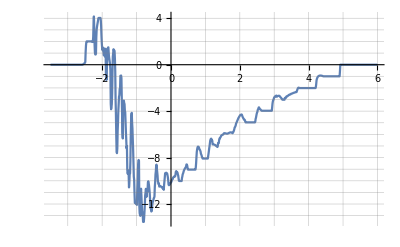

```mathematica
ListLinePlot[{sigma},GridLines->{{1,2,3,4,5,6,7,-1,-2,-3,-4,-5,-6,-7,-8,-9,-10,-11,-12,-13, -14, -15, -16,-17, -18, -19,-20}},Background->White]
```